We are considering the following association/dissociation reaction,
S+R ⇋SR

case 1: S not in excess

Solving for the dynamics

```mathematica
odes={s'[t]==-v,r'[t]==-v,sr'[t]==v};
rateeqs=v->kf s[t] r[t]-kb sr[t];
param={kf->25,kb->1};
initcond={s[0]==2,r[0]==1,sr[0]==0};
tsol=NDSolve[Join[odes/.rateeqs/.param,initcond],{s,r,sr},{t,0,100}];
```

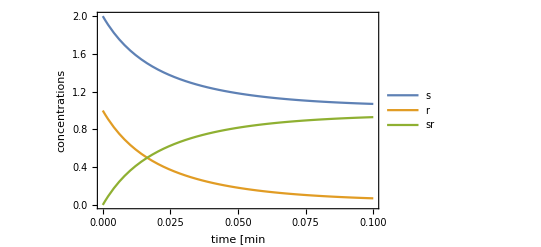

```mathematica
Plot[Evaluate[{s[t],r[t],sr[t]}/.tsol],{t,0,0.1},Frame->True,FrameLabel->{"time  [min","concentrations"},PlotLegends->{"s","r","sr"}]
```

eventually equilibrium is reached, the rate is then indeed zero

```mathematica
v/.rateeqs/.param/.t->100/.tsol
```

{0.}

the concentration are then equal to

```mathematica
{s[t],r[t],sr[t]}/.t->100/.tsol
```

{{1.03714,0.0371355,0.962864}}

Solve of the equilibrium concentrations, we find two solution sets, only of them is the correct solution.

eqsol=Solve[{0==kf s r-kb sr,sT==s+sr,rT==r+sr},{s,r,sr}]//FullSimplify

{{s→-(kb+kf rT-kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),r→-(kb-kf rT+kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),sr→(kb+kf (rT+sT)+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf)},{s→(-kb-kf rT+kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),r→(-kb+kf rT-kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),sr→(kb+kf (rT+sT)-√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf)}}

the second solution is the correct solution, which can be see from

```mathematica
eqsol/.{kf->25,kb->1,rT->1,sT->10}//N
```

{{s→-0.0444226,r→-9.04442,sr→10.0444},{s→9.00442,r→0.00442262,sr→0.995577}}

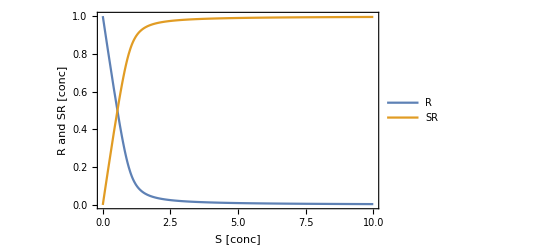

```mathematica
Plot[Evaluate[{r,sr}/.eqsol[[2]]/.{kf->25,kb->1,rT->1}],{sT,0,10},Frame->True,FrameLabel->{"S [conc]","R and SR [conc]"},PlotLegends->{"R","SR"}]
```

We can compare the analytical solution of the equilibrium with the numerical approximation and they are in agreeement

```mathematica
eqsol[[2]]/.param/.{rT->1,sT->2}//N
{s[t],r[t],sr[t]}/.t->100/.tsol
```

{s→1.03714,r→0.0371355,sr→0.962864}

{{1.03714,0.0371355,0.962864}}

```mathematica
Manipulate[Plot[Evaluate[{(-kb-kf rT+kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),(-kb+kf rT-kf sT+√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf),(kb+kf (rT+sT)-√((kb+kf (rT-sT))^2+4 kb kf sT))/(2 kf)}],{sT,0,10},Frame->True,FrameLabel->{"S [conc]","concentrations"},PlotLegends->{"S","R","SR"},PlotRange->{{0,10},{0,5}},BaseStyle->{FontSize->14}],
{{kf,25,"forward rate constant (k_f)"},0.1,50,Appearance->"Open"},
{{kb,1,"backward rate constant (k_b)"},0.1,20,Appearance->"Open"},
{{rT,1,"total receptor concentration (r_T)"},0,5,Appearance->"Open"}]
```